```mathematica
Clear[torsionConstant]
torsionConstant[region:_?RegionQ]:=Module[
{ψ,u,y,z},
ψ=NDSolveValue[{
Laplacian[u[y,z],{y,z}]==-2,
DirichletCondition[u[y,z]==0,True]
},u,{y,z}∈Ω]//Quiet;
2NIntegrate[ψ[y,z],{y,z}∈Ω]
]
```

```mathematica
Clear[crossSection]
crossSection[region:_?RegionQ,units_:"mm"]:=Module[
{data,yt,zt,y,z,colors},
data={{"Measure","Value","Units"}};

(* Area *)
AppendTo[data,{"A",Area[region],units^2}];

(* Mass center *)
{yt,zt}=NIntegrate[{y,z},{y,z}∈region]/Area[region]//Quiet;

(* Moment of inertia *)
AppendTo[data,{"I_yy",NIntegrate[(y-yt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"I_zz",NIntegrate[(z-zt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"I_yz",NIntegrate[(y-yt)(z-zt),{y,z}∈region],units^4}];
AppendTo[data,{"I_xx",NIntegrate[(y-yt)^2+(z-zt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"J_t",torsionConstant[region],units^4}];

(* Visualize *)
colors=ColorData[97,"ColorList"];
Grid[{{
Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{RGBColor["#bfbfbf"],None},{RGBColor["#f2f2f2"],None}}],
Graphics[{EdgeForm[{Thick,Opacity[0.7],colors[[1]]}],FaceForm[{Opacity[0.25],colors[[7]]}],region}]
}}]
]
```

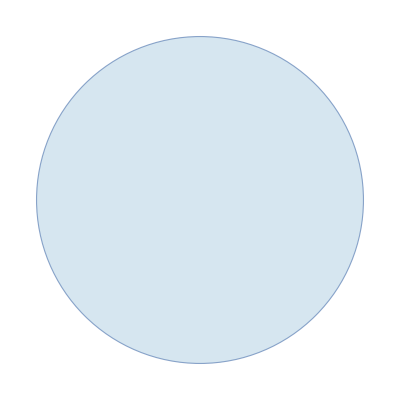
Measure | Value | Units
A | π | mm^2
I_yy | 0.785398 | mm^4
I_zz | 0.785398 | mm^4
I_yz | 0. | mm^4
I_xx | 1.5708 | mm^4
J_t | 1.57081 | mm^4 | -Graphics-

```mathematica
Ω=Disk[{0,1},1];
crossSection[Ω]
```